```mathematica
A=({{-4, 1, 0}, {0, -4, 1}, {0, 0, -4}});B=({{0, 0}, {1, 1}, {0, 0}});c=({{0, 0, 1}});d=({{0, 0}});
```

```mathematica
ssm=StateSpaceModel[{A,B,c,d}]
```

-410000-411100-40000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
{p,cssm}=ControllableDecomposition[ssm];p//MatrixForm
pᵀ.A.p//MatrixForm
cssm
```

(1 | 0
0 | 1
0 | 0)

(-4 | 1
0 | -4)

-41000-4110000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
po=NullSpace[pᵀ]ᵀ
```

{{0},{0},{1}}

```mathematica
StateSpaceTransform[ssm,ArrayFlatten[{{p,po}}]]
```

-410000-411100-40000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
cspace=ParametricPlot3D[p.{u,v},{u,-1.25,1.25},{v,-1,1},Mesh->None,PlotStyle->Opacity[0.3]]
```

-Graphics3D-

```mathematica
ssm=1-1-30-3-1305-10.1-11-1-10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic;
ControllableModelQ[ssm]
JordanModelDecomposition[ssm][[2]]
```

False

1.05+4.13491 ⅈ00-0.707107-0.162458 ⅈ01.05-4.13491 ⅈ0-0.707107+0.162458 ⅈ00-2.+0. ⅈ1.15612×10^-16+9.24899×10^-17 ⅈ-0.48319+0.974608 ⅈ-0.48319-0.974608 ⅈ-0.645655+0. ⅈ0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
{p,csys}=ControllableDecomposition[ssm];
p//MatrixForm
csys
Eigenvalues[csys[[1,1]]]
Eigenvalues[ssm[[1,1]]]
cspace=ParametricPlot3D[p.{u,v},{u,-5,5},{v,-5,5},Mesh->None,PlotStyle->Opacity[0.3]]
```

(-0.324276 | -0.628367
0.324276 | 0.628367
-0.888645 | 0.458595)

0.4995885.016940.888645-3.468341.60041-0.4585950.240094-1.715330StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

{1.05+4.13491 ⅈ,1.05-4.13491 ⅈ}

{1.05+4.13491 ⅈ,1.05-4.13491 ⅈ,-2.+0. ⅈ}

-Graphics3D-

```mathematica
x0=Flatten[Table[p.{u,v},{u,-0.8,0.8,0.3},{v,-0.8,0.8,0.3}],1];
sr=Table[StateResponse[{ssm,x},Sin[t],{t,0,10}],{x,x0}];
Show[ParametricPlot3D[Evaluate[sr],{t,0,0.5}]/.Line->Arrow,cspace]
```

-Graphics3D-

```mathematica
w=First@NullSpace[pᵀ];(* Orthogonal direction to cspace *)
x0=Flatten[Table[p.{u,v}-w,{u,-0.8,0.8,0.3},{v,-0.8,0.8,0.3}],1];
sr=Table[StateResponse[{ssm,x},Cos[2t],{t,0,10}],{x,x0}];
Show[ParametricPlot3D[Evaluate[sr],{t,0,1}]/.Line->Arrow,cspace]
```

-Graphics3D-

```mathematica
(*system test*)
q={x[t],y[t]};Fq={f[t],0}
pars={Subscript[k, 1]->75,Subscript[k, 2]->100,Subscript[m, 1]->1,Subscript[m, 2]->0.5};
T=1/2 Subscript[m, 1] x'[t]^2+1/2 Subscript[m, 2](x'[t]^2+y'[t]^2)
V = - Subscript[m, 2]g y[t]+1/2 Subscript[k, 1] x[t]^2+1/2 Subscript[k, 2] y[t]^2
L=T-V;
```

{f[t],0}

1/2 m_1 x'[t]^2+1/2 m_2 (x'[t]^2+y'[t]^2)

1/2 k_1 x[t]^2-g m_2 y[t]+1/2 k_2 y[t]^2

```mathematica
eqns=Thread[Table[D[D[L,D[s, t]],t]-D[L,s],{s,q}]==Fq]
```

{k_1 x[t]+m_1 x''[t]+m_2 x''[t]==f[t],-g m_2+k_2 y[t]+m_2 y''[t]==0}

```mathematica
ssm=StateSpaceModel[eqns,Flatten[{q,D[q, t]}],{f[t]},q,t]/.pars
```

0010000010-50.0000.6666670-200.0001000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{x[t],0},{y[t],0},x_1,x_2},{{f[t],0}},Automatic,t

```mathematica
ControllableModelQ[ssm]
```

False

```mathematica
{p,csys}=ControllableDecomposition[ssm]
```

{{{0.,-1.},{0.,0.},{1.,0.},{0.,0.}},0.50.0.666667-1.0.0.0.-1.00.0.0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1221FalseFalseFalseAutomaticNone,Automatic,{{f[t],0}},Automatic,t}

```mathematica
κc=StateFeedbackGains[csys,{-10,-15}]
```

{{37.5,-150.}}

```mathematica
κ=κc.pᵀ
```

{{150.,0.,37.5,0.}}

```mathematica
clsys=SystemsModelStateFeedbackConnect[ssm,κ]
```

0.0.1.0.00.0.0.1.0-150.0.-25.0.0.6666670.-200.0.0.01.0.0.0.00.1.0.0.0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{x[t],0},{y[t],0},x_1,x_2},{Automatic},Automatic,t

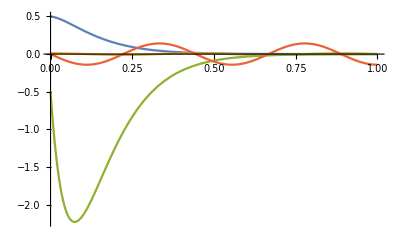

```mathematica
Plot[Evaluate[StateResponse[{clsys,{0.5,0.01,-0.5,0}},0,{t,0,7}]],{t,0,1},PlotRange->All]
```

```mathematica
(*Tracker Controller*)
csys
sspec=<|"InputModel"->csys,"TrackedOutputs"->1|>;cd =StateFeedbackGains[sspec,Table[-20-i,{i,3}], "Data"]
cd["Properties"]
```

0.50.0.666667-1.0.0.0.-1.00.0.0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1221FalseFalseFalseAutomaticNone,Automatic,{{f[t],0}},Automatic,t

SystemsModelControllerData[…]

{ClosedLoopPoles,ClosedLoopSystem,ControllerModel,Data,Design,DesignModel,FeedbackGains,FeedbackGainsModel,FeedbackInputs,InputModel,InputsCount,OpenLoopPoles,OutputsCount,OutputsCount,SamplingPeriod,StatesCount,TrackedOutputs}

{{99.,-2101.5,-15939.}}

{38033421029/384175970-9267999574/4410183StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2101FalseFalseFalseAutomaticNoneAutomatic,015939.10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{Automatic},{{e9587,0}},Automatic,Automatic}

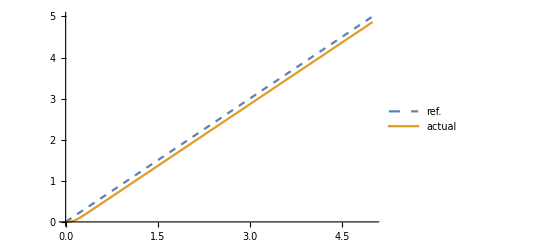

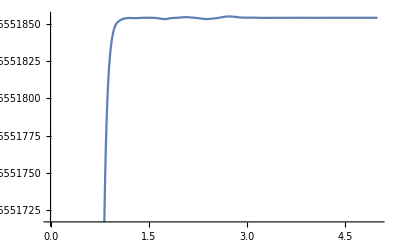

```mathematica
cd["FeedbackGains"]
cd["FeedbackGainsModel"]
ref=Ramp[t];
orp=OutputResponse[cd["ClosedLoopSystem"],ref,{t,0,5}];
Plot[{ref,orp[[1]]},{t,0,5},]
Plot[ref-orp[[1]],{t,0,5}]
```

```mathematica
(*switch to the whole system to simulate*)
κ=Flatten@cd["FeedbackGains"];
κe=Last@cd["FeedbackGainsModel"]
κx=κ[[;;-2]];
κx={κx.pᵀ}
```

015939.10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{Automatic},{{e9587,0}},Automatic,Automatic

{{2101.5,0.,99.,0.}}

```mathematica
clsysx=SystemsModelStateFeedbackConnect[ssm,κx];
clsyse=SystemsModelSeriesConnect[κe,clsysx];
clsys=SystemsModelFeedbackConnect[clsyse,{1,1}](*connect the 1 output to 1 input*)
```

0.-15939.0.0.0.15939.0.0.0.1.0.0.0.0.0.0.1.0.0.666667-1451.0.-66.0.0.0.0.-200.0.0.0.0.1.0.0.0.0.0.0.1.0.0.0.StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1251FalseFalseFalseAutomaticNone,{x_1,{x[t],0},{y[t],0},x_2,x_3},{Automatic},Automatic,t

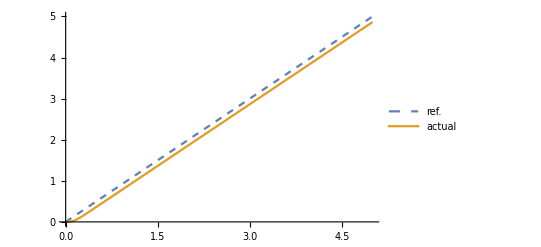

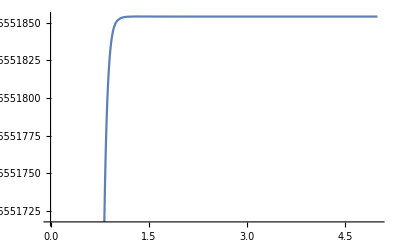

```mathematica
orp=OutputResponse[clsys,ref,{t,0,5}];
Plot[{ref,orp[[1]]},{t,0,5},]
Plot[ref-orp[[1]],{t,0,5}]
```

```mathematica
(*LQR*)
(*Tracker Controller*)
csys
sspec=<|"InputModel"->csys,"TrackedOutputs"->1|>;cd =LQRegulatorGains[sspec,{DiagonalMatrix[{50,1,100000000}],{{1}}}, "Data"]
cd["Properties"]
```

0.50.0.666667-1.0.0.0.-1.00.0.0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1221FalseFalseFalseAutomaticNone,Automatic,{{f[t],0}},Automatic,t

SystemsModelControllerData[…]

{ClosedLoopPoles,ClosedLoopSystem,ControllerModel,Data,Design,DesignModel,FeedbackGains,FeedbackGainsModel,FeedbackInputs,InputModel,InputsCount,OpenLoopPoles,OutputsCount,OutputsCount,SamplingPeriod,StatesCount,TrackedOutputs}

{{54.4366,-971.116,-10000.}}

{976930045/17946184-717522727/738864StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2101FalseFalseFalseAutomaticNoneAutomatic,010000.10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{Automatic},{{e20772,0}},Automatic,Automatic}

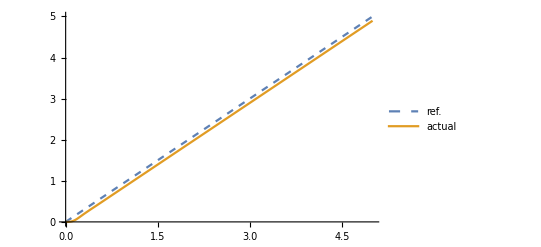

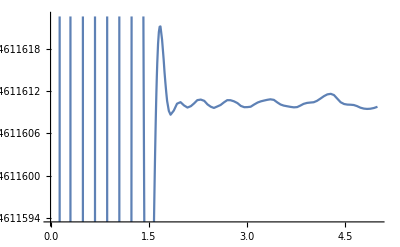

{{0.+7.07107 ⅈ,0.-7.07107 ⅈ},{-9.0913-16.8967 ⅈ,-9.0913+16.8967 ⅈ,-18.1085+0. ⅈ}}

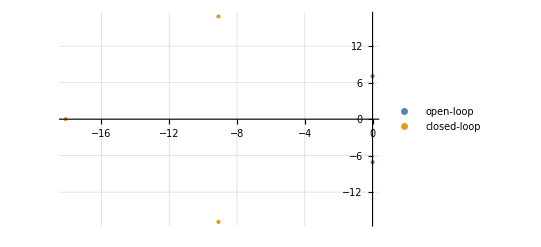

```mathematica
cd["FeedbackGains"]
cd["FeedbackGainsModel"]
ref=Ramp[t];
orp=OutputResponse[cd["ClosedLoopSystem"],ref,{t,0,5}];
Plot[{ref,orp[[1]]},{t,0,5},]
Plot[ref-orp[[1]],{t,0,5}]

poles=cd[{"OpenLoopPoles","ClosedLoopPoles"}]
ListPlot[ReIm /@ poles,]
```